# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"MH_data.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
αlist
```

{0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]}

```mathematica
clist = sims[All,#c&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"CDF_data.txt"}]];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(1/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2*Pi(Dα/μ)^(1/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
exphom[x_,coal_,μ_,Dα_:250^2/2]:=Exp[-√(μ/Dα)x]/(1+4√(μ Dα)/coal)
```

```mathematica
xlist=10^Range[-6,5.5,.33];
```

```mathematica
xlist
```

{1.×10^-6,2.13796×10^-6,4.57088×10^-6,9.77237×10^-6,0.000020893,0.0000446684,0.0000954993,0.000204174,0.000436516,0.000933254,0.00199526,0.0042658,0.00912011,0.0194984,0.0416869,0.0891251,0.190546,0.40738,0.870964,1.86209,3.98107,8.51138,18.197,38.9045,83.1764,177.828,380.189,812.831,1737.8,3715.35,7943.28,16982.4,36307.8,77624.7,165959.}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[Cos[k x]/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlist⟦;;-2⟧}]];
```

```mathematica
xmaxes=AssociationThread[αlist,{6400,3200,1600,400,200,100,30,20,8}];
```

AssociationThread::idim: {0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]} and {6400,3200,1600,400,200,100,30,20,8} must have the same length.

# Plots

## α=0.5

```mathematica
(* note that coal here is 1/rho, i.e. 1 over the population density*)
```

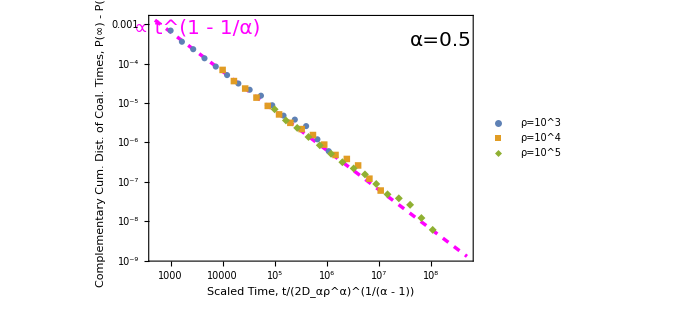

```mathematica
Module[{α=0.5, coal=.001, plotcdf, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
dummy=dummy[All,<|#,"maxcdfrho1000"-> Max[dummy[Select[#coal == .001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho10000"-> Max[dummy[Select[#coal == .0001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho100000"-> Max[dummy[Select[#coal == .00001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdf"->KroneckerDelta[#coal,.001]*#maxcdfrho1000 + KroneckerDelta[#coal,.0001]*#maxcdfrho10000 + KroneckerDelta[#coal,.00001]*#maxcdfrho100000 |>&];
dummy=dummy[All,<|#,"compcdf"->#maxcdf -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[(3.141*((1/α -1)/(Gamma[1/α +1])))^-1*x^(1-1/α),{x,500,500000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t/(2D_αρ^α)^(1/(α - 1))","Complementary Cum. Dist.
 of Coal. Times, P(∞) - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
(* Huge error bars not shown for later points.  See chart below*)
```

```mathematica
cdfsims[Select[#alpha == .5 && #coal < 10 &]]
```

Dataset[<>]

```mathematica
1/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*.01^-1*.5*(.5)^(1-.5))
```

0.00961124

```mathematica
dummy= cdfsims[Select[#alpha == .5 && #coal < 100 &]];
dummy=dummy[All,<|#,"maxcdfrho1000"-> Max[dummy[Select[#coal == .001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho10000"-> Max[dummy[Select[#coal == .0001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho100000"-> Max[dummy[Select[#coal == .00001  &],"cdf"]]|>&];
```

```mathematica
dummy
```

Dataset[<>]

```mathematica
Null
```

```mathematica
Null
```

```mathematica
maxcdf
```

0.997837

AssociationThread::idim: {0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]} and {6400,3200,1600,400,200,100,30,20,8} must have the same length.

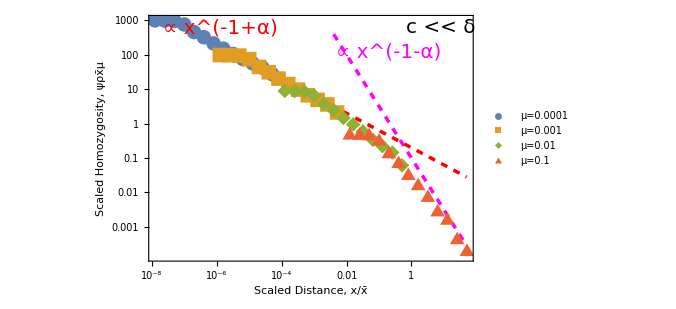

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c == .2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Sin[Pi*α/2]*Gamma[ 1-α]*(2*Pi)^-1*x^(-1+α),{x,.0001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.22,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.74,.85}]], Text[Style["c << δ",Black,20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

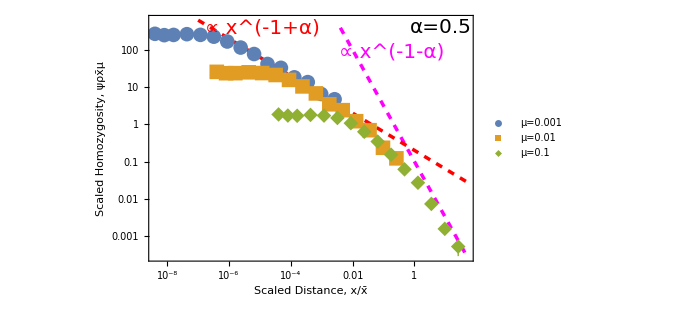

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 250&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[Sin[Pi*α/2]*Gamma[ 1-α]*(2*Pi)^-1*x^(-1+α),{x,.0000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.35,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.75,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

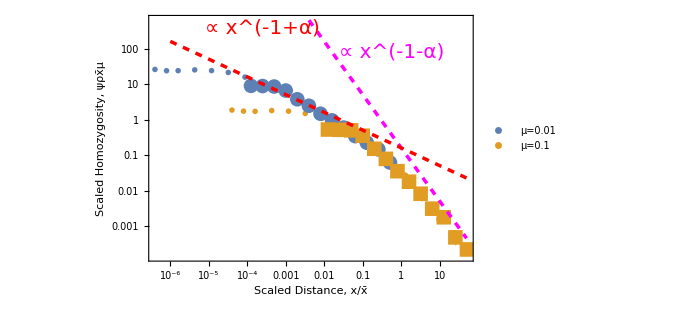

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦3;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#c ==250 &&#x0>0&]],{μ,μvals}];
plotpoints1 =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#c ==250 &&#x0>0&]],{μ,μvals}];
plotpoints2 =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c ==.2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{"OpenMarkers",12},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
ListLogLogPlot[plotpoints2,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>],ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-3,10^3.5}}],
LogLogPlot[(2*Pi)^-1*x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(2*Pi)^-1*x^(-1+α),{x,.000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
Epilog->{Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.35,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.75,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Charting`ResolvePlotTheme[Automatic,Plot]
```

{GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{AxisPadding→Scaled[0.02],DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],DefaultPlotStyle→{Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[1.6]],Directive[RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[1.6]],Directive[RGBColor[0.363898, 0.618501, 0.782349],AbsoluteThickness[1.6]],Directive[RGBColor[1, 0.75, 0],AbsoluteThickness[1.6]],Directive[RGBColor[0.647624, 0.37816, 0.614037],AbsoluteThickness[1.6]],Directive[RGBColor[0.571589, 0.586483, 0.],AbsoluteThickness[1.6]],Directive[RGBColor[0.915, 0.3325, 0.2125],AbsoluteThickness[1.6]],Directive[RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],AbsoluteThickness[1.6]],Directive[RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],AbsoluteThickness[1.6]],Directive[RGBColor[0.736782672705901, 0.358, 0.5030266573755369],AbsoluteThickness[1.6]],Directive[RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],AbsoluteThickness[1.6]]},DomainPadding→Scaled[0.02],RangePadding→Scaled[0.05]}}

```mathematica
clist
```

{0.2,179.675,250.,Missing[Empty]}

```mathematica
lineStyledimensionful={Thick,Red,Dashed};
```

```mathematica
linedelta=Line[{{.01,.001},{.01,1}}];
```

```mathematica
linecp2=Line[{{.2,0},{.2,1}}];
```

```mathematica
linec250=Line[{{250,0},{250,1}}];
```

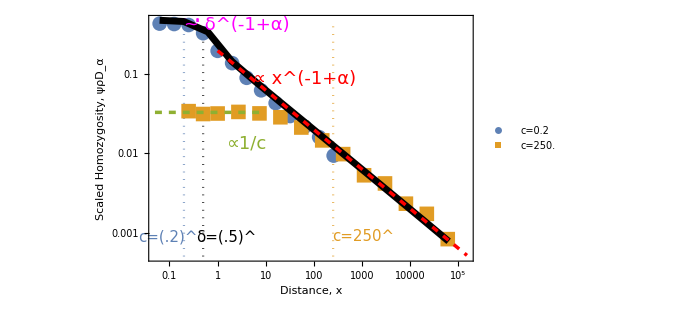

```mathematica
Module[{α=0.5,D = (250)^(.5)/2, coal =.01, plotpoints,cvals ={0.2,250.},μvals=μlist⟦2;;2⟧},
xlist2=10^Range[-11,5,.5];
intvalsfinitedelta=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(Cos[k x]*Exp[-.125*k^2/((D/.0001)^(1/.5))^2])/(1+k^α),{k,0,∞}],{x,xlist2}],{α,αlist⟦;;-2⟧}]];
plotpoints =Table[{#x0,Around[#coal^-1*(#c)^(#alpha)/2*#hom,{#coal^-1*(#c)^(#alpha)/2*#dhomLow,#coal^-1*(#c)^(#alpha)/2*#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&  #mu ==.001&&   #c == c &&#x0>0&& #x0 < 100000&]],{c,cvals}];
Show[LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ParametricPlot[{{Log[.5],Log[u]}},{u,.0005,.42},PlotStyle->{Black, Dotted}],ParametricPlot[{{Log[.2],Log[u]}},{u,.0005,.42},PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798], Dotted}],ParametricPlot[{{Log[250],Log[u]}},{u,.0005,.42},PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051], Dotted}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["c="<>ToString[#],20]&/@cvals,{.8,.9}]], ListLogLogPlot[Table[{x*(D/.0001)^(1/.5),coal^-1*D*intvalsfinitedelta[α][x]/(2*Pi*(D/.0001)^(1/.5)*coal^-1*.0001)},{x,Select[xlist2,#≤.00001&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-6,100}}],LogLogPlot[(Pi^2/6)*D*Gamma[1+1/.5]/(250*Pi),{x,.05,10},PlotStyle->{RGBColor[0.560181, 0.691569, 0.194885],Dashed,Thickness[.005]}],LogLogPlot[(Gamma[1-α]*Sin[Pi*α/2]/(2*Pi))*x^(-1+α),{x,1,150000},PlotStyle->{Red,Dashed,Thickness[.005]}],LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
Epilog->{Text[Style[" ∝ x^(-1+α) ",Red,18],Scaled[{.48,.74}]],Text[Style[" ∝1/c ",RGBColor[0.560181, 0.691569, 0.194885],18],Scaled[{.30,.48}]],Text[Style[" ~ δ^(-1+α) ",Magenta,18],Scaled[{.27,.96}]],Text[Style[" δ=(.5)^ ",Black,15],Scaled[{.24,.1}]],Text[Style[" c=(.2)^ ",RGBColor[0.368417, 0.506779, 0.709798],15],Scaled[{.06,.1}]],Text[Style[" c=250^ ",RGBColor[0.880722, 0.611041, 0.142051],15],Scaled[{.66,.1}]],Directive[lineStyledimensionful], linedelta},goodlabel["Distance, x","Scaled Homozygosity, ψρD_α",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

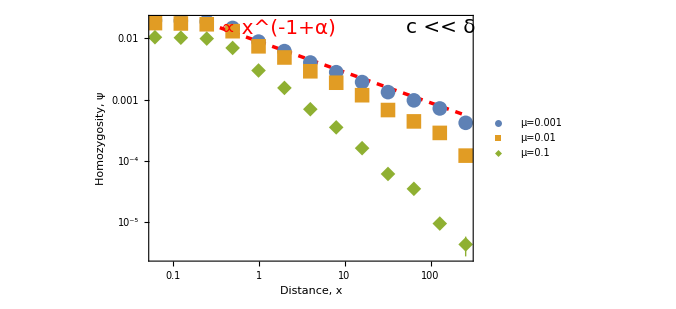

```mathematica
Module[{α=0.5,D = (.2)^(.5)/2, coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #c==.2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*D))*x^(-1+α),{x,.25,265},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.4,.95}]], Text[Style["c << δ",Black,20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

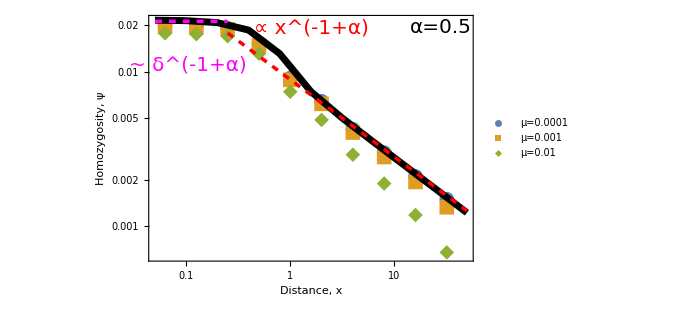

```mathematica
Module[{α=0.5,D = (.2)^(.5)/2, coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #c==.2&& #mu ==μ&&#x0>0&&#x0<50&]],{μ,μvals}];
xlist2=10^Range[-8,0,.3];
intvalsfinitedelta=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(Cos[k x]*Exp[-.125*k^2/((D/.0001)^(1/.5))^2])/(1+k^α),{k,0,∞}],{x,xlist2}],{α,αlist⟦;;-2⟧}]];
Show[
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],ListLogLogPlot[Table[{x*(D/.0001)^(1/.5),intvalsfinitedelta[α][x]/(2*Pi*(D/.0001)^(1/.5)*coal^-1*.0001)},{x,Select[xlist2,#≤.00001&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-6,10}}], LogLogPlot[coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*D))*x^(-1+α),{x,.25,50},PlotStyle->{Red,Dashed,Thickness[.005]}],  LogLogPlot[1/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*coal^-1*D*(.5)^(1-α)),{x,.05,.25},PlotStyle->{Magenta,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.5,.95}]],Text[Style[" ~ δ^(-1+α) ",Magenta,20],Scaled[{.12,.8}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
μlist[[2;;3]]
```

{0.001,0.01}

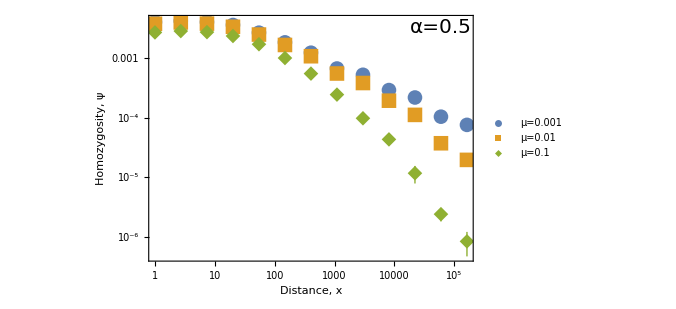

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False ]]
```

## α=.75

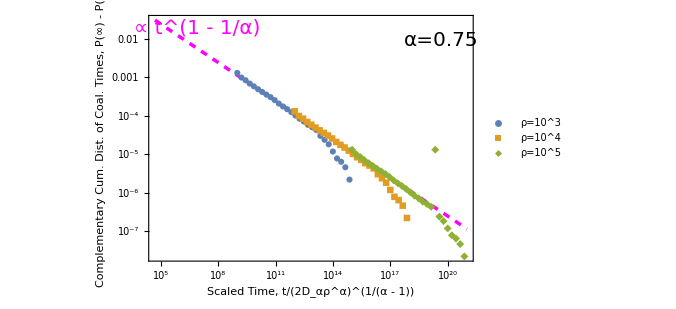

```mathematica
Module[{α=0.75, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
dummy=dummy[All,<|#,"maxcdfrho1000"-> Max[dummy[Select[#coal == .001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho10000"-> Max[dummy[Select[#coal == .0001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho100000"-> Max[dummy[Select[#coal == .00001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdf"->KroneckerDelta[#coal,.001]*#maxcdfrho1000 + KroneckerDelta[#coal,.0001]*#maxcdfrho10000 + KroneckerDelta[#coal,.00001]*#maxcdfrho100000 |>&];
dummy=dummy[All,<|#,"compcdf"->#maxcdf -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[(3.141*((1/α -1)/(Gamma[1/α +1])))^-1*x^(1-1/α),{x,50000,10^21},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.75",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t/(2D_αρ^α)^(1/(α - 1))","Complementary Cum. Dist.
 of Coal. Times, P(∞) - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
(* Huge error bars not shown for later points that trail off curve.  Deviation is withing standard error.  See chart below*)
```

```mathematica
cdfsims[Select[#alpha == .75 && #coal < 1000 &]]
```

Dataset[<>]

## α=1

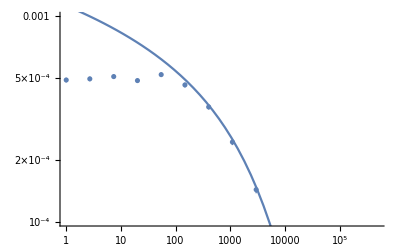

```mathematica
Module[{α=1.0, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[.05fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->{All,{-4,-3}Log[10]}]]
```

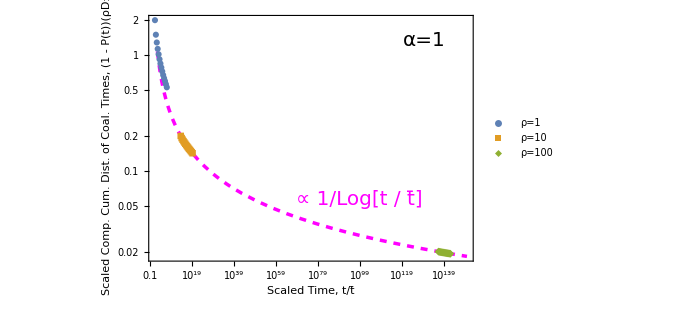

```mathematica
Module[{α=1.00, coal=1, plotcdf, c = 1,D =.5},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->((2*D)^-1*Exp[2*Pi*D/#coal])*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#coal*#compcdf/(D)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#coal*#dcdfLow/(D)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#coal*#dcdfHigh/(D)|>&];
dummy= dummy[Select[#T < 1000000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{ 1, .1, .01}}];



Show[LogLogPlot[2*Pi/Log[x],{x,10^-200,10^150},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{ "1", "10", "100"},Scaled[{.12,.2}]]],Epilog->{Text[Style["α=1",20],Scaled[{.85,.9}]],Text[Style["∝ 1/Log[t / t̄]",Magenta,20],Scaled[{.65,.25}]], ImageSize->500 },goodlabel["Scaled Time, t/t̄","Scaled Comp. Cum. Dist. of
 Coal. Times, (1 - P(t))(ρD_1)^-1",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

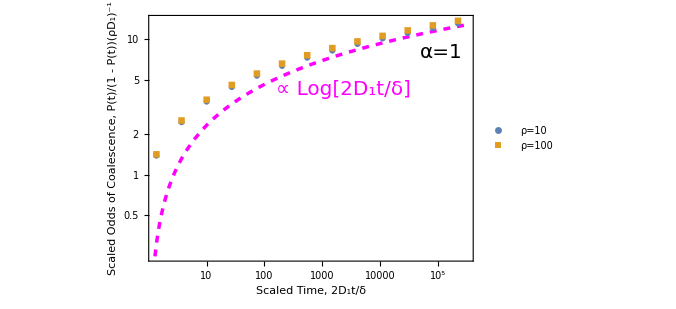

```mathematica
Module[{α=1.00, coal=1, plotcdf, c = 1,D =.5},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal && #T> 1 &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(.5*(2*D)^-1)*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->((2*Pi*(#coal)^-1*D)*( #cdf)/#compcdf)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->((2*Pi*(#coal)^-1*D)*#dcdfLow/#compcdf)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->((2*Pi*(#coal)^-1*D)*#dcdfHigh/#compcdf)|>&];
dummy= dummy[Select[#T < 1000000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{  .1, .01}}];



Show[LogLogPlot[Log[x],{x,1,10^5.5},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{  "10", "100"},Scaled[{.32,.3}]]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.85}]],Text[Style["∝ Log[2D_1t/δ]",Magenta,20],Scaled[{.6,.7}]], ImageSize->500 },goodlabel["Scaled Time, 2D_1t/δ","Scaled Odds of Coalescence, 
P(t)/(1 - P(t))(ρD_1)^-1",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

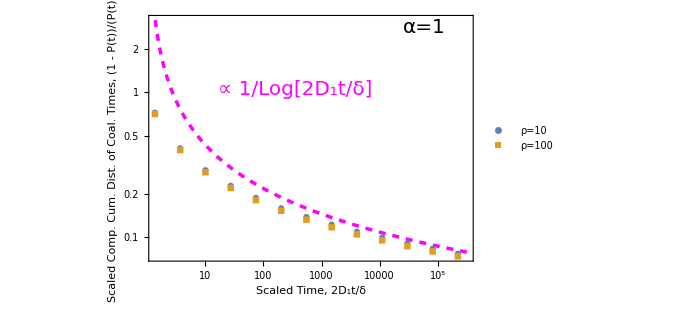

```mathematica
Module[{α=1.00, coal=1, plotcdf, c = 1,D =.5},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal && #T> 1 &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(.5*(2*D)^-1)*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->(2*Pi*(#coal)^-1*D)^-1*(#compcdf/#cdf)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->((2*Pi*(#coal)^-1*D)^-1*#dcdfLow/#cdf)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->((2*Pi*(#coal)^-1*D)^-1*#dcdfHigh/#cdf)|>&];
dummy= dummy[Select[#T < 1000000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{  .1, .01}}];



Show[LogLogPlot[1/Log[x],{x,1,10^5.5},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{  "10", "100"},Scaled[{.12,.2}]]],Epilog->{Text[Style["α=1",20],Scaled[{.85,.95}]],Text[Style["∝ 1/Log[2D_1t/δ]",Magenta,20],Scaled[{.45,.7}]], ImageSize->500 },goodlabel["Scaled Time, 2D_1t/δ","Scaled Comp. Cum. Dist. of
 Coal. Times, (1 - P(t))/(P(t)ρD_1)",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

AssociationThread::idim: {0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]} and {6400,3200,1600,400,200,100,30,20,8} must have the same length.

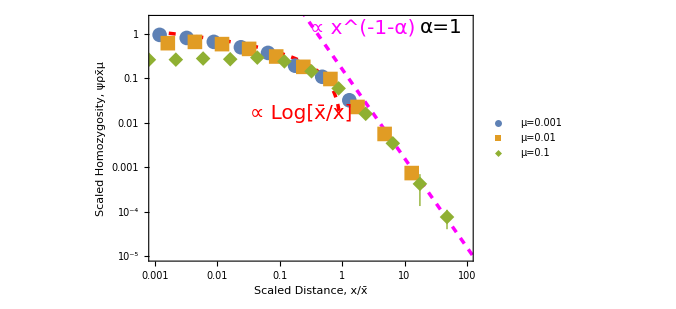

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,100},{10^-5,2}}], LogLogPlot[(2*Pi)^-1*Log[1/x],{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.001,5000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.66,.95}]], Text[Style["∝ Log[x̄/x]",Red,20],Scaled[{0.47,.6}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α = 1.25

```mathematica
250^1.25/2
```

497.044

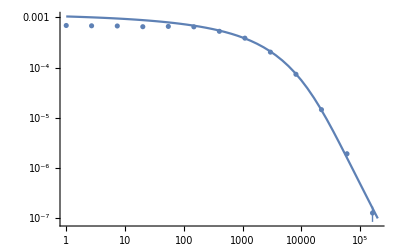

```mathematica
Module[{α=1.25, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],PlotRange->All]]
```

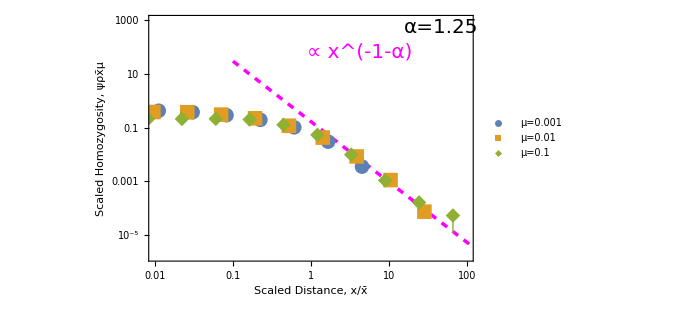

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,100},{10^-5.8,1000}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.65,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

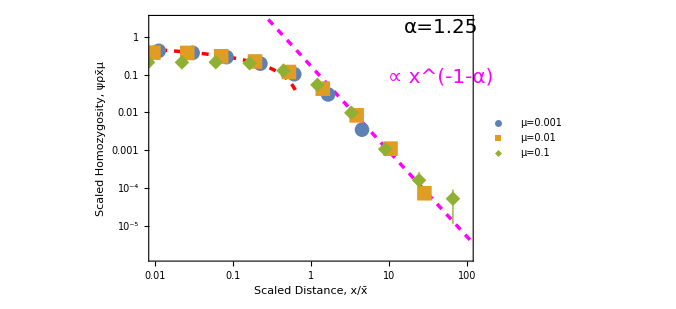

```mathematica
Module[{α=1.25,coal =.01,D=250^(α)/2, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,100},{10^-5.8,All}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

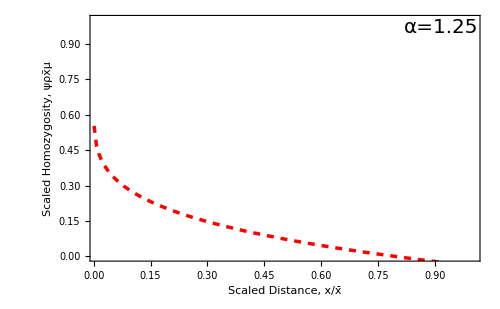

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-4.5,All}}], Plot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.45

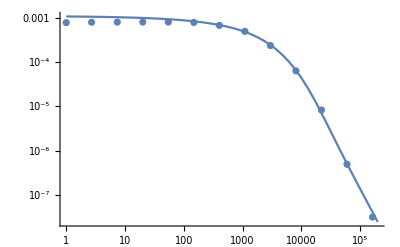

```mathematica
Module[{α=1.45, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],
PlotRange->All]]
```

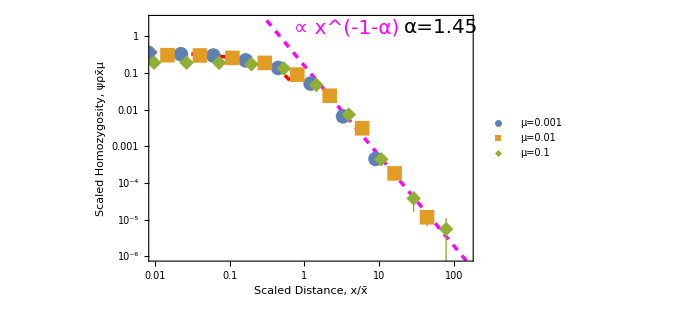

```mathematica
Module[{α=1.45,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤1.0*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,150},{10^-6,All}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,5000},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.61,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

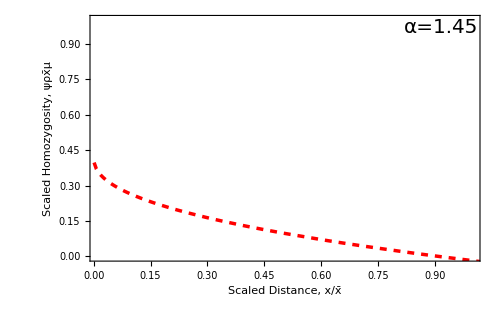

```mathematica
Module[{α=1.45,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-4.5,All}}], Plot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

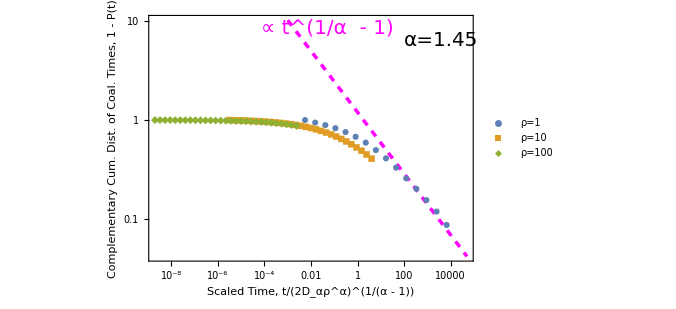

```mathematica
Module[{α=1.45, coal=.01, plotcdf, c =5, D =5^1.45/2},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"1", "10", "100"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.55,.95}]] },goodlabel["Scaled Time, t/(2D_αρ^α)^(1/(α - 1))","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=1.65

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand (0.31831 Cos[1.00024 k])/(0.01+4524.5 (0.+k)^1.65) over {0,∞}. DoubleExponentialOscillatory obtained 0.0238148 and 2.01953×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {283.95}. NIntegrate obtained 0.0238146 and 5.71187×10^-7 for the integral and error estimates.

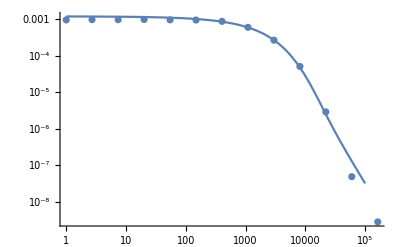

```mathematica
Module[{α=1.65, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 10^5}],
PlotRange->All]]
```

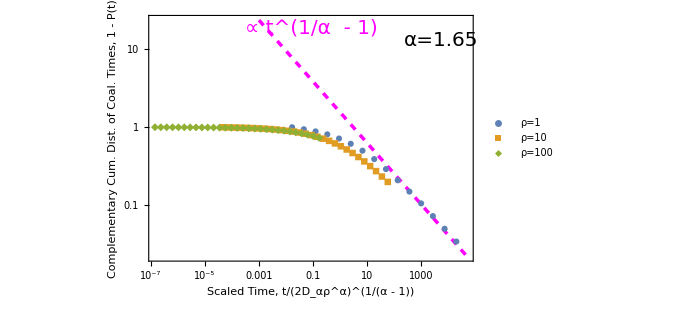

```mathematica
Module[{α=1.65, coal=.01, plotcdf, c =5, D =5^1.65/2},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"1", "10", "100"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.50,.95}]] },goodlabel["Scaled Time, t/(2D_αρ^α)^(1/(α - 1))","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

AssociationThread::idim: {0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]} and {6400,3200,1600,400,200,100,30,20,8} must have the same length.

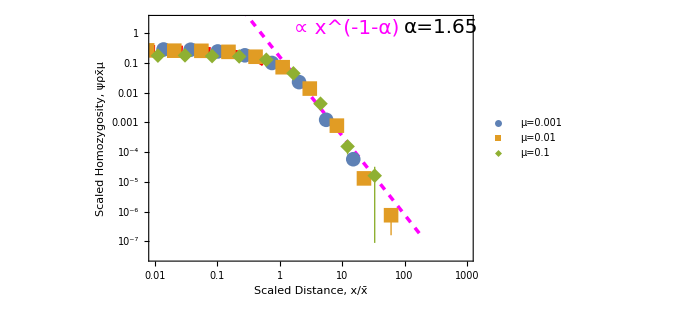

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤10*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1000},{10^-7.5,All}}], LogLogPlot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,500},PlotStyle->{Red,Dashed,Thickness[.01]}],
LogLogPlot[(2*Pi)^-1*x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.61,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

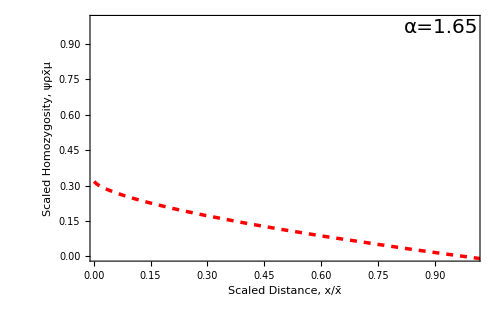

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],((2*Pi)^-1*Around[#hom,{#dhomLow,#dhomHigh}])/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-4.5,All}}], Plot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

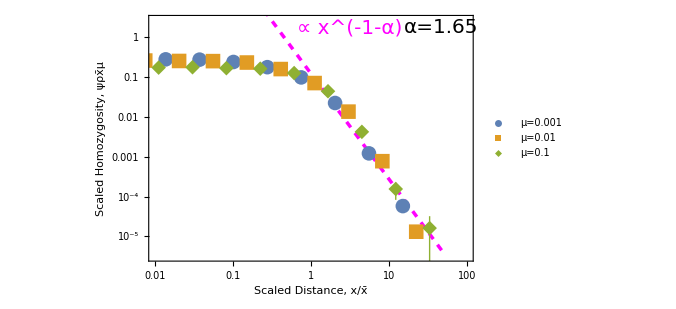

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/((2*Pi)*approxhomscale[#coal,#mu,#alpha])}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤1000*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,100},{10^-5.5,All}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.62,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.85

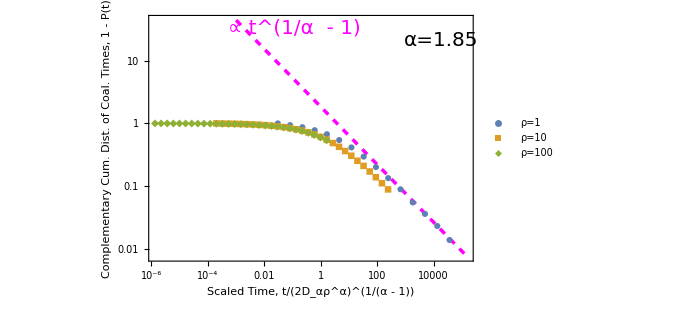

```mathematica
Module[{α=1.85, coal=.01, plotcdf, c =5, D =5^1.85/2},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,150000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"1", "10", "100"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.45,.95}]] },goodlabel["Scaled Time, t/(2D_αρ^α)^(1/(α - 1))","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

AssociationThread::idim: {0.25,0.5,0.75,1.,1.25,1.45,1.65,1.85,2.05,Missing[Empty]} and {6400,3200,1600,400,200,100,30,20,8} must have the same length.

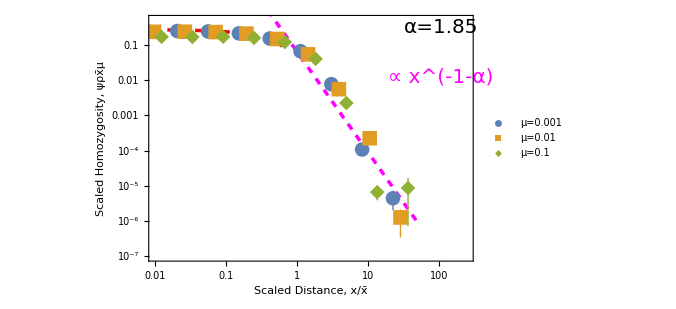

```mathematica
Module[{α=1.85,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/(2*Pi*approxhomscale[#coal,#mu,#alpha])}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,(2*Pi)^-1*intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,250},{10^-7,.5}}],
LogLogPlot[Sin[Pi*α/2]*Gamma[ α+1]*(2*Pi)^-1*x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[(1+α*Gamma[1-α]*Sin[Pi/α]/(Gamma[1-α/2]*Gamma[α/2])*x^(α-1))/(2*α*Sin[Pi/α]),{x,.001,500000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=2.05 (F distribution)

Null

```mathematica
df =0.5Module[{α=2.05},Moment[FRatioDistribution[2α,2α],2]]
```

59.5476

```mathematica
250^2.05/2
```

41185.8

```mathematica
Sin[Pi*2.05/2]
```

-0.0784591

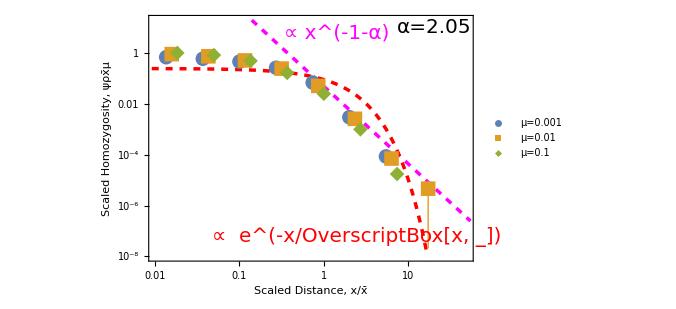

```mathematica
Module[{α=2.05,coal =.01,D=(179.675)^2/2,  plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/(√(D/#mu)),Around[#hom,{#dhomLow,#dhomHigh}]/(2*Pi*approxhomscale[#coal,#mu,2.00,D])}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0≥1&& #x0<50000&]],{μ,μvals}];
Show[LogLogPlot[(Gamma[2*α]/(4*Gamma[α]^2))*(.25*α*(2*α-1)*(α-2)^-1*(α-1)^-2+α^2/(2*α-2)^2)^(-α/2)*x^(-1-α),{x,.0001,55},PlotStyle->{{Magenta,Dashed,Thickness[.005]}},PlotRange->{{.01,50},{10^-8,20}}],LogLogPlot[Exp[-x]/(4),{x,.0001,55},PlotStyle->{{Red,Dashed,Thickness[.005]},{Red,Dotted,Thickness[.005]}},PlotRange->{{.01,10},{10^-8,20}}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=2.05",20],Scaled[{.88,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.58,0.93}]],
Text[Style["  ∝  e^(-x/OverscriptBox[x, _])",Red,20],Scaled[{.64,.1}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## All

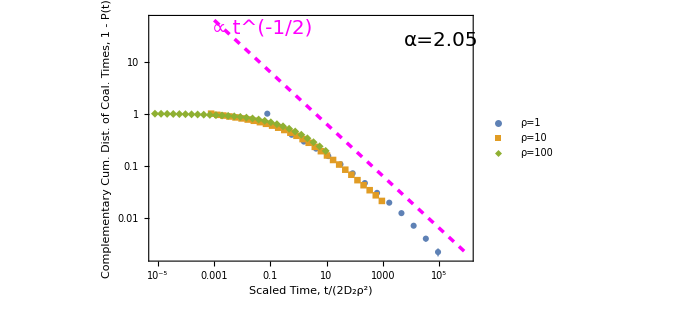

```mathematica
Module[{α=2.05, coal=.01, plotcdf, c =3.59, D =(3.59)^2/2},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-2)*D)^(1/(1 - 2))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(2*Sin[Pi/2])*x^(-1/2),{x,.001,1000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"1", "10", "100"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["∝ t^(-1/2)",Magenta,20],Scaled[{.35,.95}]] },goodlabel["Scaled Time, t/(2D_2ρ^2)","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
lineStyle={Thick,Black,Dashed};
```

```mathematica
lineStyle2={Thick, Black};
```

```mathematica
lineStyle3={Thick, Blue};
```

```mathematica
lineStyle4={Thick,Green};
```

```mathematica
lineStyle5={Thick,Red};
```

```mathematica
lineStyle6={Thick,Purple};
```

```mathematica
lineStyle7={Thick,Yellow};
```

```mathematica
lineStyle8={Thick,White};
```

```mathematica
line99=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line0=Line[{{0,0},{0,2}}];
```

```mathematica
line1=Line[{{1,0},{1,1}}];
```

```mathematica
line2=Line[{{2,0},{2,1}}];
```

```mathematica
line3=Line[{{3,0},{3,2}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line00=Line[{{0,0},{0,2}}];
```

```mathematica
line11=Line[{{1,1},{1,2}}];
```

```mathematica
line22=Line[{{2,0},{2,2}}];
```

```mathematica
line33=Line[{{3,0},{3,2}}];
```

```mathematica
line44=Line[{{0,2},{3,2}}];
```

```mathematica
line55=Line[{{0,0},{3,0}}];
```

```mathematica
line66=Line[{{0,1},{3,1}}];
```

```mathematica
line77=Line[{{0,.5},{1,.5}}];
```

```mathematica
line88=Line[{{0,.5},{3,.5}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,-2}}];
```

```mathematica
line000=Line[{{0,0},{0,-2}}];
```

```mathematica
line111=Line[{{1,0},{1,-1}}];
```

```mathematica
line222=Line[{{2,0},{2,-1}}];
```

```mathematica
line333=Line[{{3,0},{3,-2}}];
```

```mathematica
line444=Line[{{0,-2},{3,-2}}];
```

```mathematica
line555=Line[{{0,0},{3,0}}];
```

```mathematica
line666=Line[{{0,-1},{3,-1}}];
```

```mathematica
line777=Line[{{0,.3},{1,.3}}];
```

```mathematica
line888=Line[{{0,.3},{3,.3}}];
```

```mathematica
line999=Line[{{0,0},{3,0}}];
```

```mathematica
(Subscript[D, 2] μ)^(1/2)
```

√(μ D_2)

```mathematica
(Dμ)^(1/2)
```

√Dμ

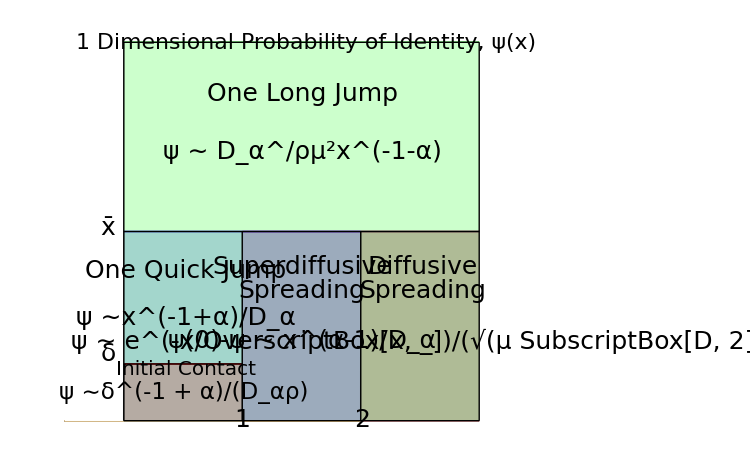

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .3*UnitStep[x] -.3*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]},{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8],Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["1",Black,25],Scaled[{.43,.020}]],Text[Style["2",Black,25],Scaled[{.71,.020}]], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ ∼ D_α^/ρμ^2x^(-1-α)",Black,25],Scaled[{.57,.70}]],  Text[Style["Superdiffusive",Black,25],Scaled[{.57,.41}]], Text[Style[" Spreading",Black,25],Scaled[{.57,.35}]],Text[Style["ψ(0)-ψ ∼ x^(α-1)/D_α",Black,25],Scaled[{.57,.22}]], Text[Style["ψ ∼x^(-1+α)/D_α",Black,25],Scaled[{.30,.28}]]  ,Text[Style["One Quick Jump",Black,25],Scaled[{.3,.40}]],Text[Style["ψ ∼δ^(-1 + α)/(D_αρ)",Black,23],Scaled[{.296,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.30,.15}]] ,Text[Style["  ψ ∼ e^(-x/OverscriptBox[x, _])/(√(μ SubscriptBox[D, 2]))",Black,25],Scaled[{.85,.22}]], Text[Style["1 Dimensional Probability of Identity, ψ(x) ",Black,22],Scaled[{.58,.98}]],Text[Style["Diffusive",Black,25],Scaled[{.85,.41}]],Text[Style[" Spreading",Black,25],Scaled[{.85,.35}]],line0, line1, line2, line3, line44, line66, line777, line999}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

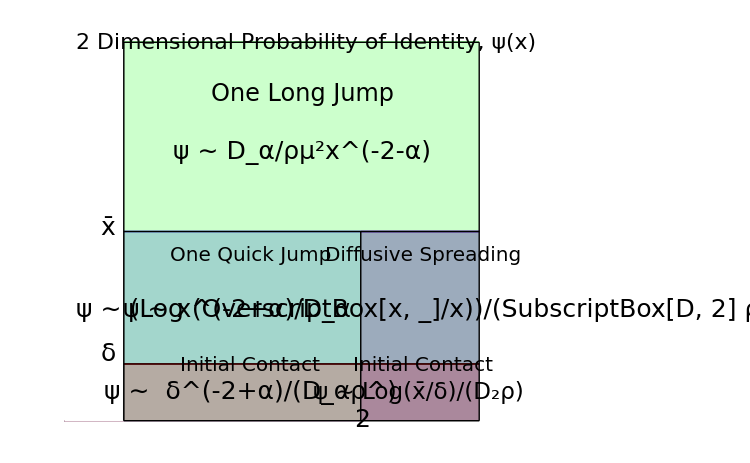

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .3*UnitStep[x], UnitStep[x -2], 0, 0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,24],Scaled[{.57,.85}]],Text[Style["ψ ∼ D_α/ρμ^2x^(-2-α) ",Black,25],Scaled[{.57,.70}]],   Text[Style["One Quick Jump",Black,20],Scaled[{.45,.44}]],Text[Style["ψ ∼ x^(-2+α)/D_α",Black,25],Scaled[{.42,.3}]], Text[Style["ψ ∼  δ^(-2+α)/(D_αρ^)",Black,25],Scaled[{.45,.09}]],Text[Style["ψ ∼ (Log (OverscriptBox[x, _]/x))/(SubscriptBox[D, 2] ρ)",Black,25],Scaled[{.85,.3}]], Text[Style["Diffusive Spreading",Black,20],Scaled[{.85,.44}]], Text[Style["Initial Contact",Black,20],Scaled[{.45,.16}]],Text[Style[" ψ ∼ Log(x̄/δ)/(D_2ρ)",Black,23],Scaled[{.84,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.85,.16}]],Text[Style[" 2 ",Black,25],Scaled[{.71,.020}]], Text[Style["2 Dimensional Probability of Identity, ψ(x) ",Black,22],Scaled[{.58,.98}]],line0, line2, line3, line44, line55, line66, line888}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

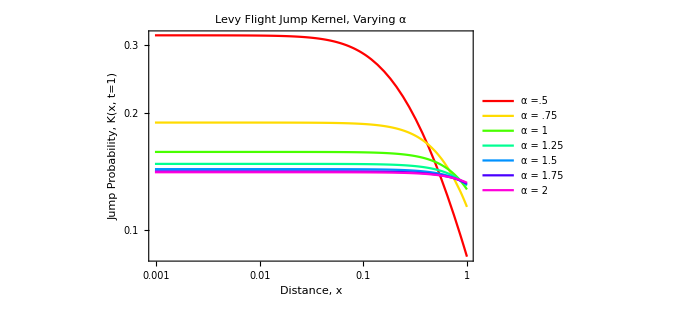

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,1}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x, t=1)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

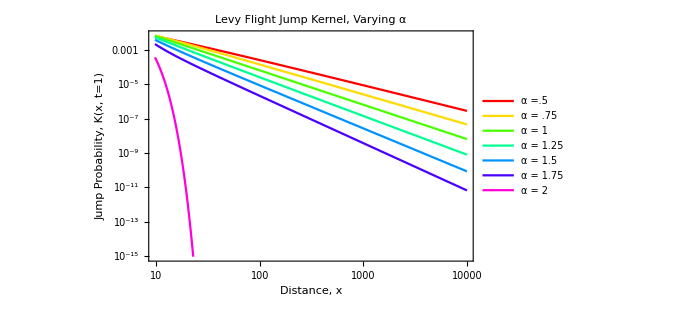

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,10000}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x, t=1)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```